# Acoustic 2D wave turbulence

## Basic definitions

```mathematica
Scol[k_,p_,q_]=k p q;
R[k_,p_,q_]=Scol[k,p,q](n[p]n[q]-n[k]n[q]-n[p]n[k])
```

k p q (-n[k] n[p]-n[k] n[q]+n[p] n[q])

```mathematica
S1k[k_]=(1/k)Integrate[R[k,k1,k-k1],{k1,0,k}]
S2k[k_]=-2 Integrate[R[k1,k,k1-k],{k1,k,Infinity}]/k
```

(∫_0^k k (k-k1) k1 (-n[k] n[k-k1]-n[k] n[k1]+n[k-k1] n[k1])ⅆk1)/k

-(2 ∫_k^∞ k k1 (-k+k1) (-n[k] n[k1]+n[k] n[-k+k1]-n[k1] n[-k+k1])ⅆk1)/k

(ⅇ^(-k/50) k^2)/250000

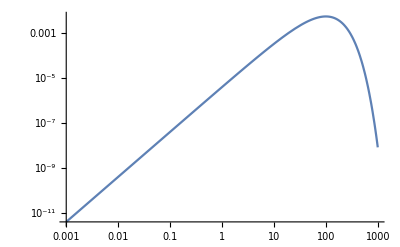

```mathematica
ntest[k_]=k^2Exp[-k/50]/250000
LogLogPlot[ntest[k],{k,1/1000,1000},PlotRange->All]
RepNk={n[k]->ntest[k],n[k1]->ntest[k1],n[k-k1]->ntest[k-k1],n[-k+k1]->ntest[-k+k1]};
```

```mathematica
Integrate[ntest[k],{k,0,Infinity}]
```

1

```mathematica
Alpha[k_]=-D[Log[ntest[k]],k]k//Expand
```

-2+k/50

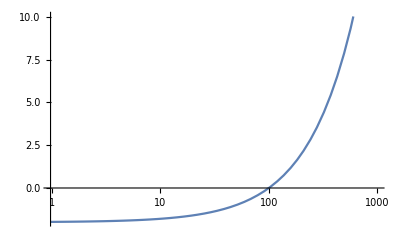

```mathematica
LogLinearPlot[Alpha[k],{k,0,1000}]
```

```mathematica
S1ttest=S1k[k]/.RepNk
S2ttest=S2k[k]/.RepNk
```

(ⅇ^(-k/25) k^2 (-700000 (3000000+45000 k+300 k^2+k^3)+ⅇ^(k/50) (2100000000000-10500000000 k+k^5)))/8750000000000

(ⅇ^(-k/25) (2 k^2 (3000000+k (45000+k (300+k)))-9375 ⅇ^(k/50) (-375000+k (-7500+k (580+3 k)))))/25000000

```mathematica
S1ttestS=Simplify[S1ttest,k>0]
S2ttestS=Simplify[S1ttest,k>0]
```

(ⅇ^(-k/25) k^2 (-700000 (3000000+45000 k+300 k^2+k^3)+ⅇ^(k/50) (2100000000000-10500000000 k+k^5)))/8750000000000

(ⅇ^(-k/25) k^2 (-700000 (3000000+45000 k+300 k^2+k^3)+ⅇ^(k/50) (2100000000000-10500000000 k+k^5)))/8750000000000

```mathematica
Integrate[S1ttest *k^2,{k,0,Infinity}]
Integrate[S2ttest *k^2,{k,0,Infinity}]
dE[q_]= Integrate[(S1ttest+S2ttest) *k^2,{k,0,q}]//Simplify//Expand
```

6542578125/2

-6542578125/2

375/8 ⅇ^(-q/50) q^3+15/16 ⅇ^(-q/50) q^4+(33 ⅇ^(-q/50) q^5)/4000-(9 ⅇ^(-q/50) q^6)/25000-(9 ⅇ^(-q/50) q^7)/8750000-(9 ⅇ^(-q/50) q^8)/3500000000-(ⅇ^(-q/50) q^9)/175000000000

```mathematica
dE[q]/ⅇ^(-q/50)//Expand
```

(375 q^3)/8+(15 q^4)/16+(33 q^5)/4000-(9 q^6)/25000-(9 q^7)/8750000-(9 q^8)/3500000000-q^9/175000000000

(ⅇ^(-k/50) (1230468750000000+24609375000000 k+196875000000 k^2-20343750000 k^3+k^7))/8750000000000

-1/175000000000 ⅇ^(-k/50) k^3 (-8203125000000+k (-164062500000+k (-1443750000+k (63000000+k (180000+k (450+k))))))

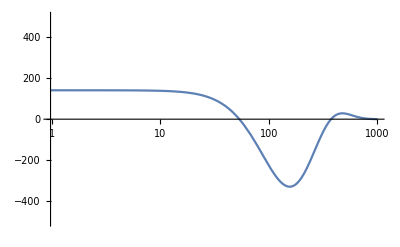

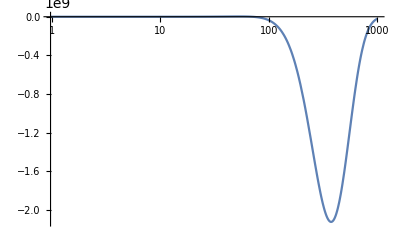

```mathematica
AlphaSk[k_]=Simplify[-D[Log[S1ttest+S2ttest],k]k];
S[k_]=S1ttest+S2ttest//Simplify
FS[k_]=Integrate[q^2S[q],{q,0,k}]//Simplify
LogLinearPlot[S[k],{k,0,1000},PlotRange->{-500, 500}]
LogLinearPlot[FS[k],{k,0,1000}]
LogLinearPlot[AlphaSk[k],{k,0,1000},PlotRange->{-2,2}];
```

## Comparing with numerics

```mathematica
j=20;
NN=40*j;
M=NN+1;
γ0=-20*j;
λ=2.^(1/(2*j));
Ik = Table[i,{i,γ0,NN+γ0}];
KK=Table[λ^Ik[[i]],{i,1,M}];
```

```mathematica
KK[[1]];
KK[[M]];
S1ttest/.k->KK[[6]]
S1ttest/.k->KK[[M-6]]
```

2.85179×10^-23

0.293568

```mathematica
S2ttest/.k->KK[[6]]
S2ttest/.k->KK[[M-6]]
```

140.625

-0.047433

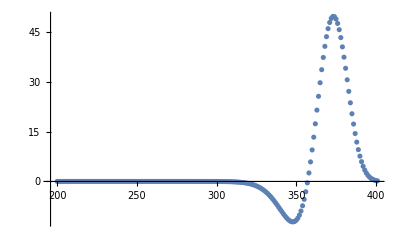

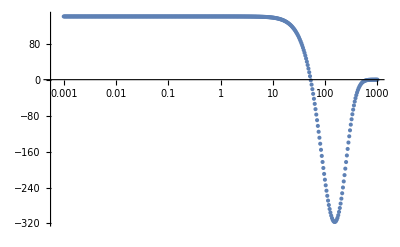

```mathematica
ListPlot[Table[{i,(S1ttest/.k->KK[[i]])},{i,200,M}],PlotRange->All]
ListLogLinearPlot[Table[{KK[[i]],(S2ttest/.k->KK[[i]])},{i,1,M}],PlotRange->All]
```

## Detailed terms

```mathematica
S1F1k[k_]= Integrate[Scol[k1,k,k-k1]ntest[k-k1]ntest[k1],{k1,0,k},Assumptions->k>0]
S1F2k[k_]=Integrate[Scol[k1,k,k-k1]ntest[k1]ntest[k],{k1,0,k},Assumptions->k>0]
S1F3k[k_]=Integrate[Scol[k1,k,k-k1]ntest[k]ntest[k-k1],{k1,0,k},Assumptions->k>0]

S2F1k[k_]=2 Integrate[Scol[k1,k,k1-k]ntest[k1-k]ntest[k],{k1,k,Infinity},Assumptions->k>0]
S2F2k[k_]=2 Integrate[Scol[k1,k,k1-k]ntest[k1]ntest[k],{k1,k,Infinity},Assumptions->k>0]
S2F3k[k_]=2 Integrate[Scol[k1,k,k1-k]ntest[k1]ntest[k1-k],{k1,k,Infinity},Assumptions->k>0]
```

(ⅇ^(-k/50) k^8)/8750000000000

(ⅇ^(-k/25) k^3 (3000000+15000 ⅇ^(k/50) (-200+k)+45000 k+300 k^2+k^3))/25000000

(ⅇ^(-k/25) k^3 (3000000+15000 ⅇ^(k/50) (-200+k)+k (45000+k (300+k))))/25000000

(3 ⅇ^(-k/50) k^3 (200+k))/2500

(ⅇ^(-k/25) k^3 (3000000+45000 k+300 k^2+k^3))/12500000

(3 ⅇ^(-k/50) k (1875000+k (37500+k (300+k))))/40000

```mathematica
Icheck=M-10;
KK[[Icheck]]
ntest[KK[[Icheck]]]
S2F1k[KK[[Icheck]]]
S2F2k[KK[[Icheck]]]
S2F3k[KK[[Icheck]]]
S2ttest/.k->KK[[Icheck]]
```

724.077

1.07739×10^-6

216.266

0.00458886

15.7892

-0.276866

```mathematica
Icheck=750;
KK[[Icheck]];
ntest[KK[[Icheck]]];
S1F1k[KK[[Icheck]]]
S1F2k[KK[[Icheck]]]
S1F3k[KK[[Icheck]]]
S1ttest/.k->KK[[Icheck]]
```

24803.7

2162.5

2162.5

48.3966

```mathematica
(S1ttest+S2ttest)/.k->KK[[Icheck]]
```

22.552

```mathematica
KK[[Icheck]]
```

401